# Subsídios para a primeira prova de Transmissão - 2010/2

O cálculo dos parâmetros é feita através da rotina que criei utilizando redução matricial para eliminação de feixes e plano complexo para solo.  Aceita solo com parâmetros variantes na frequência. As chaves são representadas como fonte de tensão controlada, quando a chave entre os nós j e k está aberta possui tensão Vjk e quando fechada Vjk=0. Os elementos não lineares não são utilizandos ainda nesse exemplo.

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[{ListPlot,ListLogLinearPlot,ListLogPlot},Frame->True,Axes->False,ImageSize->600,Joined->True,PlotStyle->{Thick},BaseStyle->{Medium,FontFamily->"Helvetica"}];
```

## Funções Auxiliares

```mathematica
μ=4 π 10^-7;
ϵ=8.854 10^-12;
```

```mathematica
(*rotinas para o calculo dos parametros unitarios de uma LT*)
inv[m_?MatrixQ,a_,b_]:=Take[Inverse[m],a,b]

eliminaPR[m_?MatrixQ,nc_,np_]:=Take[Inverse[m],nc-np,nc-np]

(*eliminacao de feixes mas a matriz deve estar como admitancia*)
eliminaFeixe[aux_?MatrixQ,nb_,nf_]:=Table[Sum[aux[[i,j]],{i,nb*m-(nb-1),nb*m},{j,nb*n-(nb-1),nb*n}],{m,nf},{n,1,nf}]

(*monta a matriz de coeficientes de potencial*)
MPot[x_?VectorQ,y_?VectorQ,nc_,npr_,rf_,rpr_]:=Table[If[i≠j,1/2 Log[((x[[i]]-x[[j]])^2+(y[[i]]+y[[j]])^2)/((x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2)],If[i≤nc-npr,Log[2 y[[i]]/rf],Log[2 y[[i]]/rpr]]],{i,1,nc},{j,1,nc}]

(*impedancia interna de condutores cilindricos*)
ZintTubo[omega_,rhoc_,rf_,ri_,mu_: 4 Pi 10^-7]:=With[{etac=Sqrt[(I omega mu)/rhoc]//N},With[{Den=BesselI[1,etac rf] BesselK[1,etac ri]-BesselI[1,etac ri] BesselK[1,etac rf],Num=(BesselI[0,etac rf] BesselK[1,etac ri]+BesselK[1,etac rf] BesselI[1,etac ri])},(rhoc etac)/(2 π rf) Num/Den]]

ZintTubo2[omega_,rhoc_,rf_,ri_,mu_: 4 Pi 10^-7]:=With[{Den=BesselI[1,Sqrt[(I omega mu)/rhoc] rf]*BesselK[1,Sqrt[(I omega mu)/rhoc] ri]-BesselI[1,Sqrt[(I omega mu)/rhoc] ri]*BesselK[1,Sqrt[(I omega mu)/rhoc] rf]//N,Num=(BesselI[0,Sqrt[(I omega mu)/rhoc] rf]*BesselK[1,Sqrt[(I omega mu)/rhoc] ri]+BesselK[1,Sqrt[(I omega mu)/rhoc] rf]*BesselI[1,Sqrt[(I omega mu)/rhoc] ri]//N)},(rhoc Sqrt[(I omega mu)/rhoc])/(2 Pi rf) Num/Den]

Zexterno[omega_,sigma_,ncond_,npr_,(x_)?VectorQ,(y_)?VectorQ,rf_,rpr_,mu_: (4*Pi)/10^7,mupr_: (4*Pi)/10^7]:=With[{p=Sqrt[1/(I*omega*mu*sigma)]},Table[If[i≠j,((I*omega*mu)/(4*Pi))*Log[((x[[i]]-x[[j]])^2+(2*p+y[[i]]+y[[j]])^2)/((x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2)],If[i≤ncond-npr,((I*omega*mu)/(2*Pi))*Log[(2*(y[[i]]+p))/rf],((I*omega*mu)/(2*Pi))*Log[(2*(y[[i]]+p))/rpr]]],{i,1,ncond},{j,1,ncond}]]


(*impedancia interna de condutores cilindricos*)

Zin[Omega_,Rhopr_,rpr_,Mur_: 80,Mupr_: (4*Pi)/10^7]:=With[{Etapr=Sqrt[(I*Omega*Mur*Mupr)/Rhopr]},((Etapr*Rhopr)*BesselI[0,Etapr*rpr])/((2*Pi*rpr)*BesselI[1,Etapr*rpr])]

(*rotinas para copiar o linspace e o logspace do matlab*)

freqlog[i_,f_,np_]:=Table[N[10^(i+(x*(f-i))/(Floor[np]-1))],{x,0,np-1}]

freqlin[i_,f_,np_]:=Table[N[i+(x*(f-i))/(Floor[np]-1)],{x,0,np-1}]

(*Calculo da matriz de admitancia nodal a partir de parametros unitarios e comprimento do circuito*)Ynodal[Z_,Y_,length_]:=Module[{Z1=Z,Y1=Y,eval,evect,d,Tv,Tvi,hm,Am,Bm,y11,y12,Yy},{eval,evect}=Eigensystem[N[Z1.Y1]];
d=Sqrt[eval];
Tv=Transpose[evect];
Tvi=Inverse[Transpose[evect]];
hm=Exp[-d*length];
Am=d*(1+hm^2)/(1-hm^2);
Bm=-2.0*d*hm/(1-hm^2);
y11=N[Inverse[Z1]].Tv.DiagonalMatrix[Am].Tvi;
y12=N[Inverse[Z1]].Tv.DiagonalMatrix[Bm].Tvi;
Yy=ArrayFlatten[{{y11,y12},{y12,y11}}]]


(*funcao para conversao de Ynodal simetrica para quadripolo*)
Y2Quad[ynodal_]:=Module[{n,y11,y12,aux,AA,BB,CC},n=Length[ynodal];
y11=ynodal[[Range[1,n/2],Range[1,n/2]]];
y12=ynodal[[Range[1,n/2],Range[n/2+1,n]]];
aux=Inverse[y12];
AA=-aux.y11;
BB=-aux;
CC=y12-y11.aux.y11;
Qout=ArrayFlatten[{{AA,BB},{CC,AA}}]]

(*funcao para conversao do quadripolo para Ynodal*)Quad2Y[quadrip_]:=Module[{n,Aeq,Beq,Ceq,Deq,aux2,yss,ysr,yrs,yrr,ynodal},n=Round[Length[quadrip]/2];
Aeq=quadrip[[Range[n],Range[n]]];
Beq=quadrip[[Range[n],Range[n+1,2*n]]];
Ceq=quadrip[[Range[n+1,2*n],Range[n]]];
Deq=quadrip[[Range[n+1,2*n],Range[n+1,2*n]]];
aux2=Inverse[Beq];
yss=Deq.aux2;
ysr=Ceq-Deq.aux2.Aeq;
yrs=-aux2;
yrr=aux2.Aeq;
ynodal=ArrayFlatten[{{yss,ysr},{yrs,yrr}}]]
```

## Configuração da LT

```mathematica
xy= {{-4.271, 10.771}, {-4.271, 11.229}, {-4.729, 11.229}, {-4.729, 10.771}, {0.229, 15.271},
{0.229, 15.729}, {-0.229, 15.729}, {-0.229, 15.271}, {4.271, 10.771}, {4.271, 11.229},{4.729, 11.229},{4.729, 10.771}, {-3.500, 26.000}, {3.500, 26.000}};
```

```mathematica
mostra1={Circle[#,.25]}&/@xy;
```

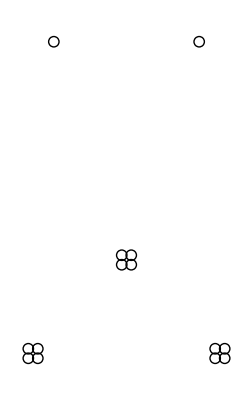

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
xc=xy[[All,1]];
```

```mathematica
yc=xy[[All,2]];
```

```mathematica
ncond=Length[xc];
npr=2;
nfeixe=4;
nfases=3;
```

```mathematica
rf=29.591*10^-3/2;
r0=(7.3914/2*10^-3);
ρc=6.114292531162*10^-5 Pi*(rf^2-r0^2);
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
ρpr=Rdcpr*Pi*rpr^2;
ρsolo=1000.;
σsolo=1/ρsolo;
```

### Resposta em Frequência

```mathematica
f=60.0;
ℓ=343/6;
nf=Length[f];
```

```mathematica
yr=1/(3+I ω 5304.4 10^-3);
zc=1-I/(ω  42017/(2 π 60.) 10^-6);
zero=DiagonalMatrix[{0,0,0}];
eye=DiagonalMatrix[{1,1,1}];
```

```mathematica
Qreator=ArrayFlatten[{{eye,zero},
                                            {DiagonalMatrix[{yr,yr,yr}],eye}}];
```

```mathematica
Qcap=ArrayFlatten[{{eye,DiagonalMatrix[{zc,zc,zc}]},
{zero,eye}}];
```

```mathematica
ϕ1={{0,1,0},{0,0,1},{1,0,0}};
```

```mathematica
Qϕ=ArrayFlatten[{{ϕ1,zero},{zero,ϕ1}}];
```

```mathematica
ylt=Table[0,{nf}];
```

```mathematica
a=Exp[I 120 Degree];
A1={{1,1,1},{1,a^2,a},{1,a,a^2}};
Aaux=ArrayFlatten[{{A1,zero},{zero,A1}}];
```

```mathematica
ω=2 π f;
aux0=DiagonalMatrix[
      Table[If[i≤(ncond-2),
        Zin[ω,ρc,rf,1.0],
        Zin[ω,ρpr,rpr,80.]],{i,ncond}]];
aux1=ⅉ ω 2.0 π ϵ eliminaPR[MPot[xc,yc,ncond,2,rf,rpr],ncond,2];
aux2=aux0+ Zexterno[ω,σsolo,ncond,2,xc,yc,rf,rpr];
Y1=eliminaFeixe[aux1,nfeixe,nfases];
Z1=Inverse[eliminaFeixe[eliminaPR[aux2,ncond,2],nfeixe,nfases]];
ylt1=Ynodal[Z1,Y1,ℓ];
Qlt1=Y2Quad[ylt1];
QLT=Qlt1.Qϕ.MatrixPower[Qlt1,2].Qϕ.MatrixPower[Qlt1,2].Qϕ.Qlt1;
yaux=Quad2Y[Qcap.Qreator.QLT.Qreator.Qcap];
ylt=Inverse[Aaux].yaux.Aaux;
```

```mathematica
Dimensions[Qlt1]
```

{6,6}

```mathematica
MatrixForm[10^3 Inverse[A1].Z1.A1//Chop]
```

(0.310463+1.48882 ⅈ | 0.00364125-0.00565505 ⅈ | -0.00671804-0.000325891 ⅈ
-0.00671804-0.000325891 ⅈ | 0.0149469+0.269742 ⅈ | -0.0151497+0.00866714 ⅈ
0.00364125-0.00565505 ⅈ | 0.0150808+0.00878648 ⅈ | 0.0149469+0.269742 ⅈ)

```mathematica
MatrixForm[10^3 Inverse[A1].Y1.A1//Chop]
```

(3.10073×10^-6 ⅈ | -1.53607×10^-7+8.86853×10^-8 ⅈ | 1.53607×10^-7+8.86853×10^-8 ⅈ
1.53607×10^-7+8.86853×10^-8 ⅈ | 6.09754×10^-6 ⅈ | 3.30484×10^-7-1.90805×10^-7 ⅈ
-1.53607×10^-7+8.86853×10^-8 ⅈ | -3.30484×10^-7-1.90805×10^-7 ⅈ | 6.09754×10^-6 ⅈ)

```mathematica
yr 10^6
```

0.750215-500.071 ⅈ